# Multi - Dimension Radon Walk

## 1 - D, 2 - Steps Random Walk

Either + a or - a
Every Step +a (chance 1/2) , or -a (chance 1/2)
Tree Diagram
the exoected Root Mean Square Distance

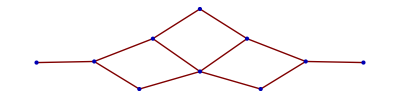

```mathematica
GraphPlot[{1->2,2->4,2->5,1->3,3->5,3->6, 4->7,4->8,5->8,5->9,6->9,6->10}]
```

```mathematica
(* the Absolute Distance after n-step, r times +a *)
AD[n_,r_]:=Abs[(r a+(n-r)(-a))]
(* The Expected AD *)
EAD[n_]:=Sum[(n!)/((n-r)!r!)1/2^n AD[n,r],{r,0,n}]
```

```mathematica
AD[2,2]
```

2 Abs[a]

```mathematica
EAD[3]/.{a->1}//N
```

1.5

```mathematica
(3 1/8+1 3/8)*2
```

3/2

```mathematica
1/(√2)//N
```

0.707107

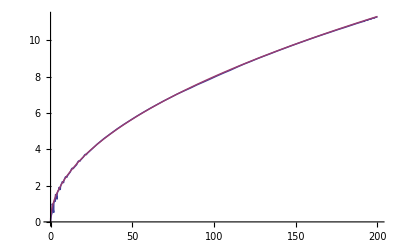

```mathematica
Plot[{Sum[(n!)/((n-r)!r!)1/2^n Abs[(r +(n-r)(-1))],{r,0,n}],0.8 √n},{n,0,200}]
```

```mathematica
Manipulate[
Plot[{(n!)/(2^n(n-r)!r!)Abs[(r +(n-r)(-1))]},{r,0,n}],{n,1,100,1}]
```

```mathematica
(* the Square Distance after n-step, r times +a *)
SD[n_,r_]:=√(r a^2+(n-r)(-a)^2)
(* The Expected AD *)
ESD[n_]:=Sum[(n!)/((n-r)!r!)1/2^n SD[n,r],{r,0,n}]
```

```mathematica
SD[3,1]/.a->1
```

√3

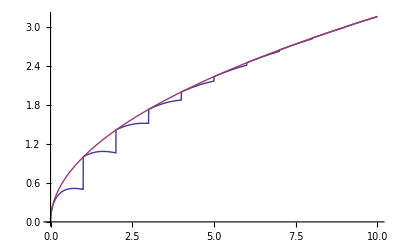

```mathematica
Plot[{Sum[(n!)/((n-r)!r!)1/2^n √(r +(n-r)),{r,0,n}],√n},{n,0,10}]
```

## 1 - D, 3 - Steps Random Walk

Either + a , 0 ,  - a
Every Step +a (chance 1/3) , 0 or -a (chance 1/3)
Tree Diagram
the exoected Root Mean Square Distance

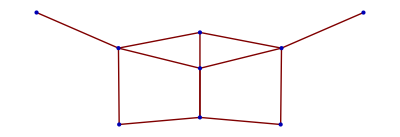

```mathematica
GraphPlot[{1->2,1->3,1->4,2->5,2->6,2->7, 3->6,3->7,3->8,4->7,4->8,4->9}]
```

```mathematica
(* the Square Distance after n-step, r1 times +a ,r2 times -a *)
SD[n_,r1_,r2_]:=√(r1 a^2+r2 a^2+(n-r1-r2)(-0)^2)
(* The Expected AD *)
ESD[n_]:=Sum[(n!)/((n-r1-r2)!r1!r2!)1/3^n SD[n,r1,r2],{r1,0,n},{r2,0,n-r1}]
```

```mathematica
ESD[20]/.(a->1)//N
```

3.63963

```mathematica
Table[ {r1,r2,3-(r1+r2)},{r1,0,3},{r2,0,3-r1}]//TableForm
```

0
0
3 | 0
1
2 | 0
2
1 | 0
3
0
1
0
2 | 1
1
1 | 1
2
0 | 
2
0
1 | 2
1
0 |  | 
3
0
0 |  |  |

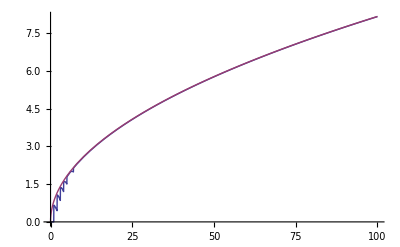

```mathematica
Plot[{Sum[(n!)/((n-r1-r2)!r1!r2!)1/3^n √(r1 +r2 +(n-r1-r2)(-0)^2),{r1,0,n},{r2,0,n-r1}],√(2/3)√n},{n,0,100}]
```

## 1 - D, 2m + 1 - Steps Random Walk

Either +ma,....+a  ,0, - a,....,-ma
Every Step +a (chance 1/(2m)) or -a (chance 1/(2m))
the expected Root Mean Square Distance

```mathematica
(* the Square Distance after n-step, r1 times +a ,r2 times -a *)
m=1;
Array[r,2m+1];
SD[n_]:=√Sum[ r[i] a^2(-m+i-1)^2,{i,1,2m+1}]
(* The Expected AD *)
ESD[n_]:=Sum[????]
```

```mathematica
ESD[n_]:=Sum[(n!)/((n-r1-r2-r3)!r1!r2!r3!)1/4^n SD[n,r1,r2,r3],{r1,0,n},{r2,0,n},{r3,0,n-r1-r2}]
```

```mathematica
Table[ {r1,r2,r3,3-(r1+r2+r3)},{r1,0,3},{r2,0,3},{r3,3-r1-r2}]//MatrixForm
```

({{0,0,1,2},{0,0,2,1},{0,0,3,0}} | {{0,1,1,1},{0,1,2,0}} | {{0,2,1,0}} | {}
{{1,0,1,1},{1,0,2,0}} | {{1,1,1,0}} | {} | {}
{{2,0,1,0}} | {} | {} | {}
{} | {} | {} | {})

## 1 - D, 2 - Steps % RW

```mathematica
(* % gain for n runs, r times gain *)
SD[n_,r_]:= (1+g)^r(1-g)^(n-r)-1
(* Expectation *)
ESD[n_]:=Sum[(n!)/((n-r)!r!)1/2^n SD[n,r],{r,n/2+1,n}]
```

```mathematica
ESD[3]/.g->0.15
```

0.0783137

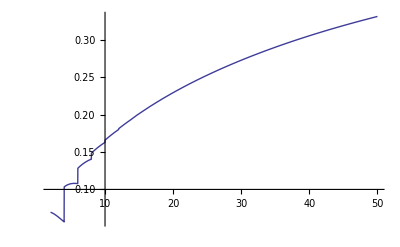

```mathematica
Plot[Sum[(n!)/((n-r)!r!)1/2^n ((1+0.15)^r(1-0.15)^(n-r)-1),{r,n/2,n}],{n,2,50}]
```